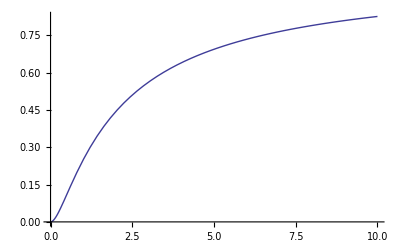

```mathematica
Needs["FunctionApproximations`"]
Plot[(x/(x+1))^2,{x,0,10}]
```

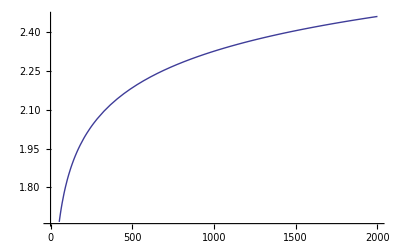

```mathematica
Plot[InverseErf[(x/(x+1))],{x,0,2000}]
```

```mathematica
MiniMaxApproximation[ x/(x+1),{x,{5,5},4,5}]
```

MiniMaxApproximation::van: Failed to locate the extrema in 20 iterations. The function x/1 + x may be vanishing on the interval {5, 5} or the WorkingPrecision may be insufficient to get convergence.

MiniMaxApproximation[x/(1+x),{x,{5,5},4,5}]

```mathematica
Plot[%38-InverseErf[1/()],{x,0.9,.99} ,PlotRange->Full]
```

-Graphics-

```mathematica
(MiniMaxApproximation[Erf[x]/x,{x,{0.0000001,3},5,6},PlotFlag->True&&PrintFlag->true&&MaxIterations->50][[2,1]])*x
```

(x (1.12838-0.90402 x+0.381049 x^2-0.0527095 x^3-0.00496157 x^4+0.00196384 x^5))/(1-0.801178 x+0.671197 x^2-0.314803 x^3+0.122569 x^4-0.0288088 x^5+0.00333155 x^6)

```mathematica
CDF[NormalDistribution[0,1]]
```

1/2 Erfc[(0-#1)/(√2 1)]&

```mathematica
MiniMaxApproximation[1/2 Erfc[-x/(√2)],{x,{0,5},4,5},Brake->{10,10}&&MaxIterations->500][[2,1]]
```

MiniMaxApproximation::conv: Warning: convergence was not complete.

(0.500006+0.258306 x+0.0131948 x^2+0.0067541 x^3+0.013347 x^4)/(1-0.28077 x+0.247371 x^2-0.0444257 x^3+0.0189689 x^4-0.00024807 x^5)

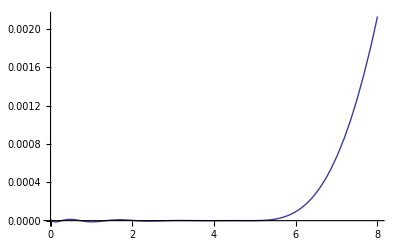

```mathematica
Plot[Log[%23/(1/2 Erfc[-x/(√2)])],{x,0,8} ,PlotRange->Full]
```

```mathematica
floom[y]
```

```mathematica
psi=HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.1,5},3,5},Bias->-0][[2,1]]*x]
```

(x (-664.282+x (211.052+(-54.6369-3.13535 x) x)))/(-1665.13+x (529.232+x (-414.991+x (80.874+x (-28.0145+1. x)))))

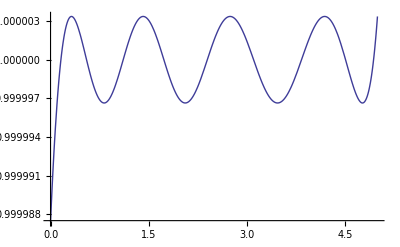

```mathematica
Plot[psi/(1/2 Erfc[-x/(√2)]-1/2),{x,0,5}]
```

```mathematica
HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.05,5},4,5}][[2,1]]*x]
```

(x (-6738.03+x (2057.05+x (-551.013+(-30.5159-4.29621 x) x))))/(-16889.6+x (5153.98+x (-4185.16+x (762.029+x (-271.851+1. x)))))

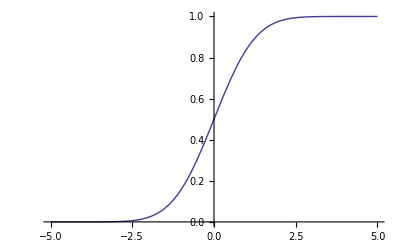

```mathematica
Plot[(1/2 Erfc[-x/(√2)]),{x,-5,5}]
```

```mathematica
GeneralMiniMaxApproximation[{(psi-1/2)/x,x}, {x,{0.1,0.99},5,7},x][[2,1]]
```

GeneralMiniMaxApproximation::van: Failed to locate the extrema in 20 iterations. The weight function x may be vanishing on the interval {0.1, 0.99}, or the WorkingPrecision may be insufficient to get convergence.

x